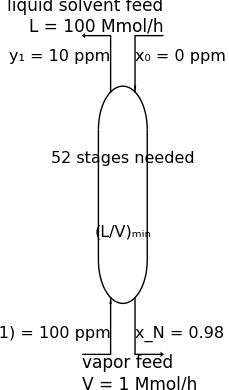

```mathematica
Module[{h,w,ry},
h=10;w=15;ry=2;

Graphics[{Thick,
Line[{{#,ry},{#,h-ry}}]&/@{0,w},Circle[{w/2,ry},{w/2,ry},{π,2*π}],Circle[{w/2,h-ry},{w/2,ry},{0,π}],
(*****************)
Text[Style["52 stages needed",16],{0.5*w,0.666*h}],
Text[Style[Subscript[Row@{"(",Style["L",Italic],"/",Style["V",Italic],")"},"min"],16],{0.5*w,0.33*h}],

Arrowheads@0.1,
Arrow[{{0.25*w,h/1.03},{0.25*w,h+h/4.3},{-w/3,h+h/4.3}}],
Arrow[{{-w/3,h-h/0.81},{0.25*w,h-h/0.81},{0.25*w,0.03*h}}],
Arrow[{{w+w/3,h+h/4.3},{0.75*w,h+h/4.3},{0.75*w,h/1.03}}],
Arrow[{{0.75*w,0.03*h},{0.75*w,h-h/0.81},{w+w/3,h-h/0.81}}],

Text[Style["y_1 = 10 ppm",16,Background->White],{0.25*w,(h+h/4.3+h/1.03)/2},{0.5,-0.5}],
Text[Style["y_(N + 1) = 100 ppm",16,Background->White],{0.25*w,(h-h/0.81+0.03*h)/2},{0.5,1}],
Text[Style["x_0 = 0 ppm",16,Background->White],{0.75*w,(h+h/4.3+h/1.03)/2},{-0.5,-0.75}],
Text[Style["x_N = 0.98 ppm",16,Background->White],{0.75*w,(h-h/0.81+0.03*h)/2},{-0.5,1}],

Text[Style[Column[{"liquid solvent feed",Row@{Style["L",Italic]," = 100 Mmol/h"}},Right],17],{w+w/3,h+h/4.3},{1,-1.5}],
Text[Style[Column[{"vapor feed",Row@{Style["V",Italic]," = 1 Mmol/h"}},Left],17],{-w/3,h-h/0.81},{-1,1.5}]

},ImageSize->{230,390},AspectRatio->Full,PlotRangePadding->{None,Scaled@0.01}]
]
```